{{-0.0273893,0.999625},{-0.783363,0.621565},{-0.999085,0.0427605}}

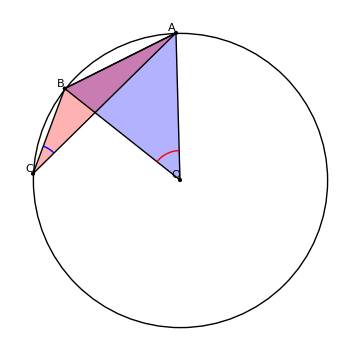

{{-0.0273893,0.999625},{-0.783363,0.621565},{-0.999085,0.0427605}}

```mathematica
(* PIANO B con GRAPHICS*)
circleCenter = {0,0};
(* 1. generare angoli alla circonferenza partendo da angolo al centro*)
alpha =  ((Mod[input , 180]/. input -> 50)/.value_/; value == 0 -> 180)°;

AAngle = RandomReal[{0, Pi}]; 
circAngle = RandomReal[{alpha + 0.1, 2*Pi - 0.1 }];

points = {CirclePoints[{1, AAngle}, 1][[1]]};
AppendTo[points,  RotationMatrix[alpha].points[[1]]];
(*beta = (360 - 2*alpha)/2; *)
beta = 180°- alpha;
choices = { RandomChoice[{-1, 1}] *(alpha/2 + 0.1+RandomReal[{0, beta  - 0.1}]),alpha/2 + beta +RandomReal[{0, alpha}]};

(*RadioButtonBar[Dynamic[choice], {2 -> "Interno",  1 -> "Esterno"}]*)

choice=1;
AppendTo[points,RotationMatrix[choices[[choice]]].middlePoint/.middlePoint->RotationMatrix[alpha/2].points[[1]]]
(*AppendTo[points,RotationMatrix[Dynamic[choices[[choice]]]].middlePoint/. middlePoint ->  RotationMatrix[alpha/2].points[[1]]];*)

Graphics[{
Circle[circleCenter, 1] ,
Point[circleCenter],
Point /@ points,

{Opacity[0.3],Style[Triangle[{points[[1]],points[[2]],circleCenter}], Blue]},
{Opacity[0.3],Style[Triangle[points], Red]},

Line[Append[points,  points[[1]]]],(* triangolo con angolo al centro *)
Line[{points[[1]],points[[2]],circleCenter, points[[1]]}], (* triangolo con angolo alla circonferenza *)

Tooltip[Style[Circle[circleCenter, 0.2, {AAngle, AAngle + alpha}], Red, Thick ], alpha],
Tooltip[Style[Circle[points[[3]], 0.2, {angletemp, angletemp+alpha/2}], Blue, Thick ], alpha/2],
(* Annotation[Style[Circle[points[[3]], 0.2, {angletemp, angletemp+alpha/2}], Blue, Thick ], alpha/2, "Mouse"], *)

MapIndexed[ Text[FromCharacterCode[#2[[1]]+ 64] , #1, {1.5,-1.5}]&, points], 
Text["O", circleCenter,{1.5,-1.5}]
}, ImageSize -> Medium]/.{angletemp -> PlanarAngle[points[[3]] -> { {points[[3]][[1]] + 1, points[[3]][[2]]}, points[[1]]}]}

(*Angolo : Dynamic[MouseAnnotation[]] *)
Dynamic[choice]
points
```